```mathematica
(*constants*)
ACC = 10000;
HWCap = 2.4*10^-3 ;(*nF*)
BIOCap =0.24; (*nF*)
vShift = 1200;
vAlpha = 10;
```

```mathematica
(*invers calibration*)
invEl[V_] := 0.9804 * V + 8.4118;
invVthr[V_] := 1.002*V + 3.5571;
invIglPLUS[x_] := (-0.24 +Sqrt[0.0576 - 2.208*10^-4*(0.89 - x)]) / (1.104 * 10^-4) ;
invIglMINUS[x_] := (-0.24 -Sqrt[0.0576 - 2.206*10^-4*(0.89 - x)]) / (1.164 * 10^-4) ;
invIpl[x_] := 40/x + 0.016;
invIgladaptPLUS[x_] := (-0.26 +Sqrt[0.0676 + 1.972*10^-4*(0.66 + x)]) / (9.86 * 10^-5) ;
invIgladaptMINUS[x_] := (-0.26 -Sqrt[0.0676 + 1.972*10^-4*(0.66 + x)]) / (9.86 * 10^-5) ;
invIradaptPLUS[x_] := (0.00032 + Sqrt[1.024*10^-7 - 1.76*10^-5 * (0.0005 + 1/x)])/(8.8*10^-6);
invIradaptMINUS[x_] := (0.00032 - Sqrt[1.024*10^-7 - 1.76*10^-5 * (0.0005 + 1/x)])/(8.8*10^-6);
invIfirePLUS[x_] := (45 + Sqrt[2025+0.56*(54.75 - x)])/0.28;
invIfireMINUS[x_] := (45 - Sqrt[2025+0.56*(54.75 - x)])/0.28;
invIrexpPLUS[x_] := (-66.3847 + Sqrt[4406.9265 + 36.9544 * (x  + 94.2541)])/18.4772;
invIrexpMINUS[x_] := (-66.3847 - Sqrt[4406.9265 + 36.9544 * (x  + 94.2541)])/18.4772;
invVexp[V_] := 2.6882*V - 269.597;
invVsyntcPLUS[x_] := (37 + Sqrt[1369 - 15.76*(x - 1382)])/7.88;
invVsyntcMINUS[x_] := (37 - Sqrt[1369 - 15.76*(x - 1382)])/7.88;
```

```mathematica
(*invers scaling*)
rescaleV[V_] := (V- vShift)/vAlpha;
rescaleCurrent[x_] := x * BIOCap / ( ACC * vAlpha * HWCap);
rescaleDeltaT[x_] := x  /10;
rescaleConductance[x_] := x*BIOCap / (ACC * HWCap);
rescaleTau[x_] := x * ACC / 1000;
```

```mathematica
(*invers transformations*)
invtransEl[V_] := rescaleV[invEl[V]];
invtransVthr[V_] := rescaleV[invVthr[V]];
invtransIglPLUS[x_] := rescaleConductance[invIglPLUS[x]];
invtransIglMINUS[x_] := rescaleConductance[invIglMINUS[x]];
invtransIpl[x_] := rescaleTau[invIpl[x]];
invtransIgladaptPLUS [x_]:= rescaleConductance[invIgladaptPLUS[x]];
invtransIgladaptMINUS [x_]:= rescaleConductance[invIgladaptMINUS[x]];
invtransIradaptPLUS[x_] := rescaleTau[invIradaptPLUS[x]];
invtransIradaptMINUS[x_] := rescaleTau[invIradaptMINUS[x]];
invtransIfirePLUS[x_] := rescaleCurrent[invIfirePLUS[x]];
invtransIfireMINUS[x_] := rescaleCurrent[invIfireMINUS[x]];
invtransIrexpPLUS[x_] := rescaleDeltaT[invIrexpPLUS[x]];
invtransIrexpMINUS[x_] := rescaleDeltaT[invIrexpMINUS[x]];
invtransVexp[V_] := rescaleV[invVexp[V]];
invtransVsyntcPLUS[x_] := rescaleTau[invVsyntcPLUS[x]];
invtransVsyntcMINUS[x_] := rescaleTau[invVsyntcMINUS[x]];
```

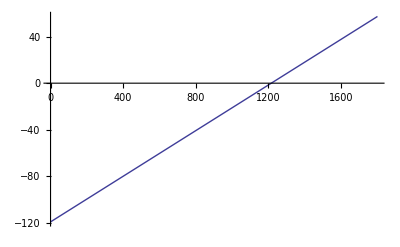

```mathematica
(*Plots*)
(*LIF dynamics*)
Plot[invtransEl[V],{V,0,1800}]
```

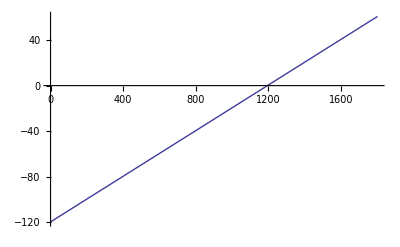

```mathematica
Plot[invtransVthr[V],{V,0,1800}]
```

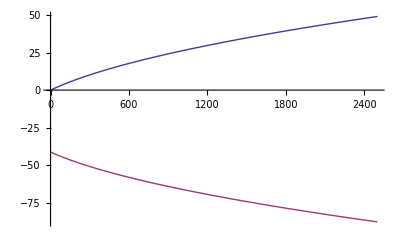

```mathematica
Plot[{invtransIglPLUS[x],invtransIglMINUS[x]},{x,0,2500}] (*PLUS is the physical solution*)
```

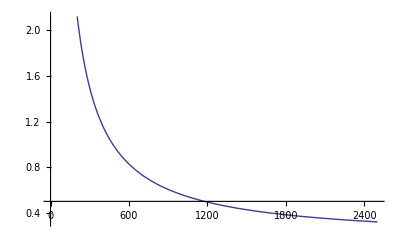

```mathematica
Plot[invtransIpl[x],{x,0,2500}]
```

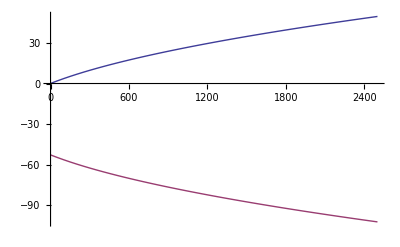

```mathematica
(*Adaptation term*)
Plot[{invtransIgladaptPLUS[x],invtransIgladaptMINUS[x]},{x,0,2500}] (*PLUS is the physical solution*)
```

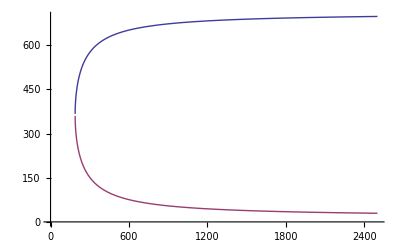

```mathematica
Plot[{invtransIradaptPLUS[x],invtransIradaptMINUS[x]},{x,0,2500}](*MINUS is the physical solution*)
```

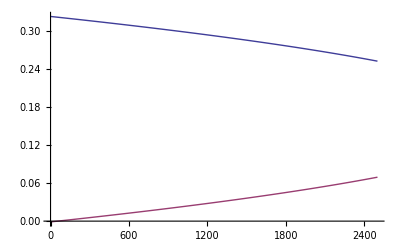

```mathematica
Plot[{invtransIfirePLUS[x], invtransIfireMINUS[x]}, {x,0,2500}] (* MINUS is the physical solution*)
```

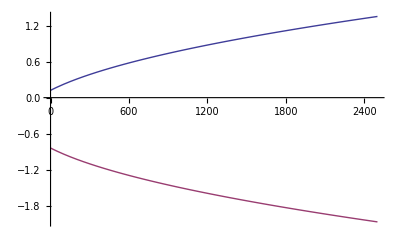

```mathematica
(*Exponential term*)
Plot[{invtransIrexpPLUS[x], invtransIrexpMINUS[x]}, {x,0,2500}] (*PLUS is the physical solution*)
```

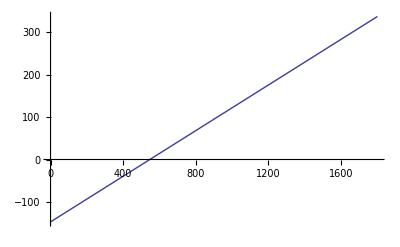

```mathematica
Plot[invtransVexp[V], {V,0,1800}] (*passt*)
```

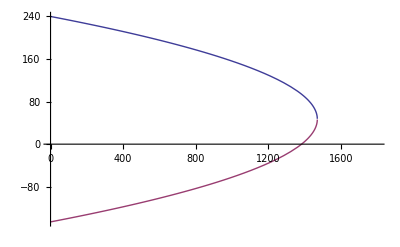

```mathematica
(*synaptic Input*)
Plot[{invtransVsyntcPLUS[x],invtransVsyntcMINUS[x]} , {x,0,1800}](*MINUS is the physical solution)
```

```mathematica
(*data for test*)
dacmvolt[x_] := x * 1800/1023;
daccurr[x_] := x * 2500 / 1023;
```

```mathematica
invtransEl[dacmvolt[511]]
```

-31.0091

```mathematica
invtransIglPLUS[daccurr[511]]
```

30.5414

```mathematica
BIOCap / 30.5414 * 1000
```

7.85819

```mathematica
invtransIgladaptPLUS[daccurr[511]]
```

30.4612

```mathematica
invtransIradaptMINUS[daccurr[511]]
```

43.2176

```mathematica
invtransIrexpPLUS[daccurr[511]]
```

0.898815

```mathematica
invtransIfireMINUS[daccurr[511]]
```

0.0291836

```mathematica
invtransVsyntcMINUS[dacmvolt[800]]
```

7.52924

```mathematica
invtransVexp[dacmvolt[511]]
```

94.7418

```mathematica
invtransIpl[daccurr[511]]
```

0.480313

```mathematica
invtransVthr[dacmvolt[511]]
```

-29.5524